```mathematica
F[con_,x_]:=Module[{m=Length[con]},
For[i=1,i≤m,i++,
If[Mod[x,m]==i-1,
a=con[[i,1]];b=con[[i,2]];Return[a x+b]]]]
```

```mathematica
collatz={{1/2,0},{3,1}}
```

{{1/2,0},{3,1}}

```mathematica
A117248[x_]:=F[{{1/2,1},{1,-1}},x-1]
```

```mathematica
Table[A117248[x],{x,4,20}]
```

{2,3,4,4,6,5,8,6,10,7,12,8,14,9,16,10,18}

```mathematica
Table[F[{{1/2,0},{2,1}},x],{x,-10,10}]
```

{-5,-17,-4,-13,-3,-9,-2,-5,-1,-1,0,3,1,7,2,11,3,15,4,19,5}

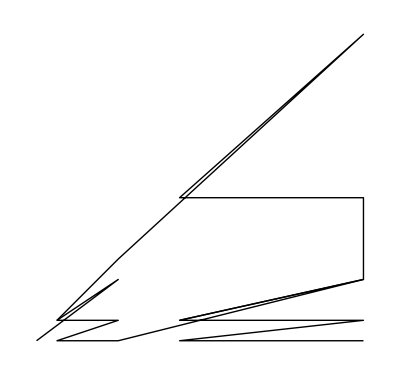

```mathematica
Graphics[{Line[{{2,1},{6,4},{3,2},{6,2},{3,1},{6,1},{18,4},{9,2},{18,2},{9,1},{18,1}}],Line[{{3,2},{6,5},{18,16},{9,8},{18,8},{18,4},{9,2}}]}]
```

```mathematica
3x+2
```

2+3 x

```mathematica
3(2a)+2
```

20

```mathematica
3(2n)+2
```

2+6 n

```mathematica
3n+1
```

1+3 n